```mathematica
Quit
```

```mathematica
LGet["ExFactorial"]
ClearSystemCache[];CC
```

所有临时定义已清空!

```mathematica
MultiFactorial[3k,3,Complex->True]
MultiFactorial[3k,3]
```

1/(2 Gamma[1/3] Gamma[2/3])3^(1/3 (-5+3 k)) Gamma[1+k] (6 Gamma[1/3]+6 Cos[2/3 (1+3 k) π] Gamma[1/3]+6 Cos[4/3 (1+3 k) π] Gamma[1/3]+6 3^(1/3) Gamma[2/3]-3 3^(1/3) Cos[4 k π] Gamma[2/3]+6 3^(1/3) Cos[2/3 (2+3 k) π] Gamma[2/3]+2 3^(2/3) Gamma[1/3] Gamma[2/3]+2 3^(2/3) Cos[2 k π] Gamma[1/3] Gamma[2/3]+2 3^(2/3) Cos[4 k π] Gamma[1/3] Gamma[2/3]-3 3^(5/6) Gamma[2/3] Sin[4 k π])

3^Quotient[2+3 k,3] Binomial[k,Quotient[2+3 k,3]] Quotient[2+3 k,3]!

```mathematica
Unprotect[FunctionExpand,AlternatingFactorial];
SetAttributes[
{
HyperFactorial,SuperFactorial,
SubFactorial,
EulerFactorial,HadamardFactorial,LuschnyFactorial
},
{NumericFunction,Listable}
]

HyperFactorial[n_?NumericQ]:=Hyperfactorial[n]
SuperFactorial[n_?NumericQ]:=BarnesG[n+2]
FunctionExpand[HyperFactorial[z_]]:=Hyperfactorial[z]
FunctionExpand[SuperFactorial[z_]]:=BarnesG[z+2]

(*AlternatingFactorial*)
(*Format[AlternatingFactorial[z_],TraditionalForm]:=RowBox[{"AF(",MakeBoxes[z,TraditionalForm],")"}]*)
SubFactorial[n_?NumericQ]:= Subfactorial[n]
FunctionExpand[SubFactorial[z_]]:=Subfactorial[z]

RisingFactorial[x_?NumericQ,n_?NumericQ]:=Pochhammer[x,n]
FallingFactorial[x_?NumericQ, n_?NumericQ] := (-1)^n Pochhammer[-x, n]
FunctionExpand@RisingFactorial[x_,n_]:=Pochhammer[x,n]
FunctionExpand@FallingFactorial[x_, n_] := (-1)^n Pochhammer[-x, n]

EulerFactorial[x_?NumericQ]:=Gamma[x+1]
HadamardFactorial[x_?NumericQ]:=(PolyGamma[1/2-x/2]-PolyGamma[-x/2])/(2Gamma[-x])
LuschnyFactorial[x_?NumericQ]:=(1/2+x(PolyGamma[1-x/2]-PolyGamma[1/2-x/2])/2)/(-x)!
FunctionExpand@EulerFactorial[x_]:=Gamma[x+1]
FunctionExpand@HadamardFactorial[x_]:=(PolyGamma[1/2-x/2]-PolyGamma[-x/2])/(2Gamma[-x])
FunctionExpand@LuschnyFactorial[x_]:=(1/2+x(PolyGamma[1-x/2]-PolyGamma[1/2-x/2])/2)/(-x)!
```

```mathematica
Series[FunctionExpand@LuschnyFactorial[x],{x,0,3}]
```

1/2+(-EulerGamma-1/2 PolyGamma[0,1/2]) x+1/24 (18 EulerGamma^2+π^2+12 EulerGamma PolyGamma[0,1/2]) x^2+1/48 (-16 EulerGamma^3-12 EulerGamma^2 PolyGamma[0,1/2]+2 π^2 PolyGamma[0,1/2]-3 PolyGamma[2,1/2]+7 PolyGamma[2,1]) x^3+O[x]^4

```mathematica
Table[SuperFactorial[n],{n,10}]//TT
Table[Product[k!,{k,n}],{n,10}]//TT
```

总运行时:  0.00054724

CPU 时间:  0.

{1,2,12,288,34560,24883200,125411328000,5056584744960000,1834933472251084800000,6658606584104736522240000000}

总运行时:  0.0000713792

CPU 时间:  0.

{1,2,12,288,34560,24883200,125411328000,5056584744960000,1834933472251084800000,6658606584104736522240000000}

```mathematica
Format[AlternatingFactorial[n+1],TraditionalForm]=.
Format[AlternatingFactorial[z_],TraditionalForm]:=RowBox[{"AF(",MakeBoxes[z,TraditionalForm],")"}]
```

```mathematica
CC
```

所有临时定义已清空!

```mathematica
Quit
```

```mathematica
TraditionalForm[Style[x^3+y^3==22 z^3,FontSize->24]]
```

x^3+y^3==22 z^3

```mathematica
AlternatingFactorial//PDL
```

函数查询:  AlternatingFactorial

```mathematica
AlternatingFactorial[e_] := Block[{val = System`BarnesDump`af2af2System`BarnesDump`af2 @ e}, val /; UnsameQ[val, $Failed]];
```

```mathematica
HoldPattern[Except[AlternatingFactorial[_], AlternatingFactorial[args___]]] := Condition[
	Null,
	ArgumentCountQ[AlternatingFactorial, Length @ {args}, 1, 1]
];
```

```mathematica
Attributes[AlternatingFactorial] := {Listable, NumericFunction, Protected, ReadProtected};
```

```mathematica
AlternatingFactorial[___][___] := «kernel function»;
```

```mathematica
MakeBoxes[RisingFactorial[z_Symbol,n_],TraditionalForm]:=SuperscriptBox[MakeBoxes[z,TraditionalForm],MakeBoxes[OverBar@n,TraditionalForm]]
MakeBoxes[RisingFactorial[z_,n_],TraditionalForm]:=SuperscriptBox[RowBox[{"(",MakeBoxes[z,TraditionalForm],")"}],MakeBoxes[OverBar@n,TraditionalForm]]

RisingFactorial[1,n]//HoldForm//TraditionalForm
```

(1)^(n̄)

```mathematica
D[RisingFactorial[x,n]//FunctionExpand,x]
```

Pochhammer[x,n] (-PolyGamma[0,x]+PolyGamma[0,n+x])

```mathematica
FallingFactorial[x_, n_] := (-1)^n Pochhammer[-x, n]
MakeBoxes[FallingFactorial[z_Symbol,n_],TraditionalForm]:=SuperscriptBox[MakeBoxes[z,TraditionalForm],MakeBoxes[Style[n,Underlined],TraditionalForm]]
MakeBoxes[FallingFactorial[z_,n_],TraditionalForm]:=SuperscriptBox[RowBox[{"(",MakeBoxes[z,TraditionalForm],")"}],MakeBoxes[Style[n,Underlined],TraditionalForm]]
RSolve[{x a[x,n]==a[x,n+1]+n a[x,n],a[x,0]==1},a[x,n],n]
FallingFactorial[x,n]//HoldForm//TraditionalForm


RisingFactorial[x,0]
```

{{a[x,n]→(-1)^(1+n) x Pochhammer[1-x,-1+n]}}

x^n

1

```mathematica
FullSimplify
```

```mathematica
CC
```

所有临时定义已清空!

```mathematica
PosIntQ=IntegerQ@#&&#>0&;
ExpFactorial[0]:=1
ExpFactorial[n_?PosIntQ]:=ExpFactorial[n]=n^(ExpFactorial[n-1])
RSolve[{a[n]==n^a[n-1],a[1]==1},a[n],n]

Primorial[0]:=1
Primorial[1]:=2
Primorial[n_?PosIntQ]:=Primorial[n]=Prime[n]Primorial[n-1]

ExpFactorial[4]
```

RSolve[{a[n]==n^a[-1+n],a[1]==1},a[n],n]

262144

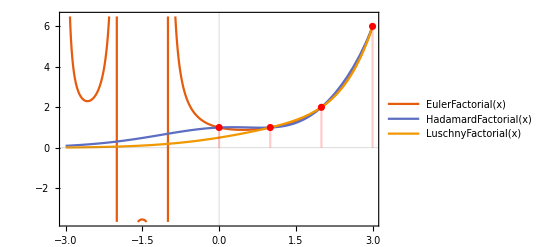

```mathematica
con=Plot[{EulerFactorial[x],HadamardFactorial[x],LuschnyFactorial[x]},{x,-3,3},PlotLegends->"Expressions",PlotTheme->"Scientific"];
dis=DiscretePlot[n!,{n,0,3},PlotStyle->Red];
Show[con,dis]
```

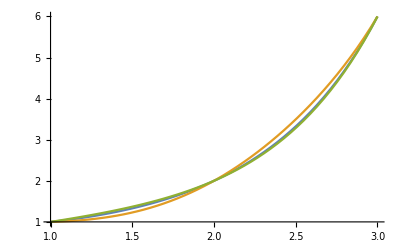

```mathematica
Plot[Evaluate[{EulerFactorial[x],HadamardFactorial[x],LuschnyFactorial[x]}-0x!],{x,3,1}]
```

```mathematica
7^n*Gamma[n+1/7]/Gamma[1/7]
```

(7^n Gamma[1/7+n])/Gamma[1/7]

```mathematica
Table[(2^n Gamma[1/2+n])/Gamma[1/2],{n,1,20}]//FullSimplify
```

{1,3,15,105,945,10395,135135,2027025,34459425,654729075,13749310575,316234143225,7905853580625,213458046676875,6190283353629375,191898783962510625,6332659870762850625,221643095476699771875,8200794532637891559375,319830986772877770815625}

```mathematica
Table[Factorial2[n],{n,1,20}]
```

{1,2,3,8,15,48,105,384,945,3840,10395,46080,135135,645120,2027025,10321920,34459425,185794560,654729075,3715891200}

```mathematica
ComplexFnPlot[f_,range_,options___]:=Block[{rangerealvar,rangeimagvar,g},g[r_,i_]:=(f/.range[[1]]:>r+I i);
Plot3D[Abs[g[rangerealvar,rangeimagvar]],{rangerealvar,Re[range[[2]]],Re[range[[3]]]},{rangeimagvar,Im[range[[2]]],Im[range[[3]]]},options,ColorFunction->(Hue[Mod[Arg[g[#1,#2]]/(2*Pi)+1,1]]&),ColorFunctionScaling->False]]
```

```mathematica
ComplexFnPlot[Gamma[z],{z,-3.5-5.5I,3.5+5.5I},PlotRange->{0,4},MaxRecursion->4,Mesh->All]
```

-Graphics3D-

```mathematica
With[{pr=FoldList[Times,1,Prime@Range[20]]},Table[pr[[PrimePi[n]+1]],{n,0,40}]]
```

{1,1,2,6,6,30,30,210,210,210,210,2310,2310,30030,30030,30030,30030,510510,510510,9699690,9699690,9699690,9699690,223092870,223092870,223092870,223092870,223092870,223092870,6469693230,6469693230,200560490130,200560490130,200560490130,200560490130,200560490130,200560490130,7420738134810,7420738134810,7420738134810,7420738134810}